# Slipping of a rectangle plane

## Initialization Notation

```mathematica
(*get association of resources,name of local host and remove local host from available resources*)
(*hosts=Counts[ReadList[Environment["NODEFILE"],"String"]]
local=First[StringSplit[Environment["HOSTNAME"],"."]]
hosts[local]--;
(*launch subkernels and connect them to the controlling Wolfram Kernel*)
Needs["SubKernels`RemoteKernels`"];
Map[If[hosts[#]>0,LaunchKernels[RemoteMachine[#,"ssh -x -f -l `3` `1` /gpfs/runtime/opt/mathematica/12.0/Executables/wolfram -wstp -linkmode Connect `4` -linkname '`2`' -subkernel -noinit",hosts[#]]]]&,Keys[hosts]];
dir=DirectoryName[$InputFileName];*)
```

```mathematica
Unprotect[Out];
$HistoryLength=0;
ParallelEvaluate[$HistoryLength=0];
<<NDSolve`FEM`
dir=NotebookDirectory[];
SetDirectory[dir]
```

/Users/wenqiangfang/Dropbox (Brown)/Research/Synthetic_Plasticity

```mathematica
ClearAll[PlotMeshBC]
Protect[ShowMesh,ShowNumbers,ShowBCs];
Options[PlotMeshBC]={ShowMesh->False,ShowNumbers->False,ShowBCs->False};
PlotMeshBC[mesh_,DirichletPoints_,NeumannPoints_,OptionsPattern[]]:=
If[OptionValue[ShowMesh],
Block[{PltPoints,plt},
Switch[OptionValue[ShowBCs]
,"DirichletBC"
,PltPoints =Cases[DirichletPoints,{#,_}][[;;,2]]&/@Range[ndof];
plt = True;
,"NeumannBC"
,PltPoints =Cases[NeumannPoints,{#,_}][[;;,2]]&/@Range[ndof];
plt = True;
,False
,plt =False;];
Show[
Join[{mesh["Wireframe"]}
,
If[OptionValue[ShowNumbers]
,{mesh["Wireframe"["MeshElement" -> "MeshElements","MeshElementIDStyle"->Blue]]
,mesh["Wireframe"["MeshElement" -> "PointElements","MeshElementIDStyle"->Red]]},{}]
,
If[plt
,Switch[ndof
,2,{Graphics[{PointSize[Large],Orange,Point[Coords[[PltPoints[[1]]]]]}]
,Graphics[{PointSize[Large],Green,Point[Coords[[PltPoints[[2]]]]]}]}
,3,{Graphics3D[{PointSize[Large],Orange,Point[Coords[[PltPoints[[1]]]]]}]
,Graphics3D[{PointSize[Large],Green,Point[Coords[[PltPoints[[2]]]]]}]
,Graphics3D[{PointSize[Large],Purple,Opacity[0.3],Point[Coords[[PltPoints[[3]]]]]}]}
],{}]
]
,ViewPoint->{1.5,1,1},BaseStyle->{FontSize->20}]
],Null];

PrintBB[X_List]:=Block[{},
Print[Sequence@@(Style[#,Blue,Bold]&/@X)];
]
PrintRB[X_List]:=Block[{},
Print[Sequence@@(Style[#,Red,Bold]&/@X)];
]
```

## Problem Solution: Numerics

### Boundary condition

```mathematica
ClearAll[DefineBCs,Edgedet];
DefineBCs[uVec_,tVec_,L_,r_]:=
Block[{tol=10^-5,IDArray},
DirichletPoints=Block[{Bttm,BttmRit,Lft,Bck,Rit,RitBttm,Tp,Nodes},
(*Bttm =Flatten@Position[Abs[Coords[[;;,3]]-0.0],x_/;x<tol];*)
Lft=Flatten@Position[Abs[Coords[[;;,2]]-(-r)],x_/;x<tol];
Bck=Flatten@Position[Abs[Coords[[;;,1]]-(-r)],x_/;x<tol];
(*Nodes = Join[{1,#}&/@Bck,{2,#}&/@Lft,{3,#}&/@Bttm]*)
Nodes = Join[{1,#}&/@Bttm,{2,#}&/@Bttm(*,{3,#}&/@Bttm*)]
(*Nodes = Join[{1,#}&/@Extract[Rit,RitBttm],{2,#}&/@Extract[Bttm,BttmRit],{2,#}&/@Tp]*)
];
DirichletDof = Sort[(DirichletPoints[[;;,2]]-1)*ndof+DirichletPoints[[;;,1]]];
NeumannPoints=Block[{Tp,Rit,Frnt,ETp,ERit,EFrnt,Nodes},
(*Tp=Flatten@Position[Abs[Coords[[;;,3]]-L],x_/;x<tol];*)
Rit=Flatten@Position[Abs[Coords[[;;,2]]-(r)],x_/;x<tol];
Frnt=Flatten@Position[Abs[Coords[[;;,1]]-(r)],x_/;x<tol];
ETp=Edgedet@{0,0,-1};
ERit=Edgedet@{0,-1,0};
EFrnt=Edgedet@{-1,0,0};
Edges=Join[{1,#}&/@EFrnt,{2,#}&/@ERit,{3,#}&/@ETp];
(*Nodes =  {3,#}&/@Tp*)
Nodes = Join[{1,#}&/@Frnt,{2,#}&/@Rit,{3,#}&/@Tp]
];
NeumannDof= Sort[(NeumannPoints[[;;,2]]-1)*ndof+NeumannPoints[[;;,1]]];
DirichletVals=uVec[[#[[1]]]][Coords[[#[[2]]]]]&/@DirichletPoints;
NeumannVals=tVec[[#[[1]]]][Coords[[#[[2]]]]]&/@NeumannPoints;
IDArray=Range[ndof*nnp];
IDMat=Transpose[ArrayReshape[IDArray,{nnp,ndof}]];
IDno=Complement[IDArray,DirichletDof];
]
Edgedet[n_,mesh_]:=Extract[mesh["BoundaryElements"][[1,1]],Position[Map[Norm@(#-n)&,mesh["BoundaryNormals"][[1]]],x_/;x<10^-5]];
DefineBCs1[uVec_,tVec_,L_]:=
Block[{tol=10^-5,IDArray},
DirichletPoints=Block[{Bttm,BttmRit,Lft,Bck,Rit,RitBttm,Tp,Nodes},
Bttm =Flatten@Position[Abs[Coords[[;;,2]]-0.0],x_/;x<tol];
Nodes = Join[{1,#}&/@Bttm,{2,#}&/@Bttm]
];
DirichletDof = Sort[(DirichletPoints[[;;,2]]-1)*ndof+DirichletPoints[[;;,1]]];
NeumannPoints=Block[{Tp,Rit,Frnt,ETp,ERit,EFrnt,Nodes},
Tp=Flatten@Position[Abs[Coords[[;;,2]]-L],x_/;x<tol];
Nodes =  {1,#}&/@Tp
];
NeumannDof= Sort[(NeumannPoints[[;;,2]]-1)*ndof+NeumannPoints[[;;,1]]];
DirichletVals=uVec[[#[[1]]]][Coords[[#[[2]]]]]&/@DirichletPoints;
NeumannVals=tVec[[#[[1]]]][Coords[[#[[2]]]]]&/@NeumannPoints;
IDArray=Range[ndof*nnp];
IDMat=Transpose[ArrayReshape[IDArray,{nnp,ndof}]];
IDno=Complement[IDArray,DirichletDof];
]
```

### Apply Traction

```mathematica
ClearAll[ApplyTraction];
SetAttributes[ApplyTraction,HoldFirst];
ApplyTraction[rMat_,edge_]:=
Block[{
ElementType=Head@BoundaryElements[[1]],
integrationOrder,
ELEtMat=ConstantArray[0.0,{ndof,nsen}]
,OutEdge,coord,jacobi,ELEt,Q
,GuassPointsNatural,GuassWeights,NMat,dN,NetTrctn
},
integrationOrder=If[ElementType===QuadElement,2elementOrder,elementOrder];
GuassPointsNatural=ElementIntegrationPoints[ElementType,integrationOrder];
GuassWeights=ElementIntegrationWeights[ElementType,integrationOrder];
NMat=ElementShapeFunction[ElementType,elementOrder];
dN= ElementShapeFunctionDerivative[ElementType,elementOrder];
(*OutEdge=Flatten[Outer[List,Range[ndof],Edge],1];*)
OutEdge={edge[[1]],#}&/@edge[[2]];
coord =Coords[[edge[[2]]]];
jacobi =If[ndof==3,Norm[Cross@@((dN@@#).coord)]&
,Norm[(dN@@#).coord]&];
ELEtMat=ReplacePart[ELEtMat,edge[[1]]->Map[NeumannBC,OutEdge]];
(*ELEtMat=ArrayReshape[ReplacePart[Map[NeumannBC,OutEdge],Position[KeyExistsQ[NeumannBC,#]&/@OutEdge,False]->0.0],{ndof,nsen}];*)
ELEt=jacobi[#](ELEtMat.NMat@@#)&;
NetTrctn=GuassWeights.(ELEt/@GuassPointsNatural);
Q=Flatten@IDMat[[;;,edge[[2]]]];
rMat[[Q]]+=Flatten[ConstantArray[#/nsen,nsen]&/@NetTrctn];
]
```

### Neo-Hookean Constitutive law

```mathematica
Kirchhoff[e0_,BMat:_,ELEu:_,ξ_List]:=
Block[{e=e0
,F,J,B,TrB,σ,τ
,Ε,ν,Κ,λ,μ},
{Ε,ν,Κ,λ,μ}=MaterialProperty;
F=ℐ+BMat[ξ].ELEu;
J=Det[F];
B=F.Transpose[F];
TrB = If[ndof==3,Tr[B],Tr[B]+1];(*difference in 3D and 2D*)
σ= μ/J^(5/3)(B-TrB/3 ℐ)+Κ(J-1)ℐ;
τ = J σ
]

Tangent[e0_,BMat:_,ELEu:_,ξ_List]:=
Block[{e=e0
,F,J,B,TrB,σ,τ
,Ε,ν,Κ,λ,μ},
{Ε,ν,Κ,λ,μ}=MaterialProperty;
F=ℐ+BMat[ξ].ELEu;
J=Det[F];
B=F.Transpose[F];
TrB = If[ndof==3,Tr[B],Tr[B]+1];(*difference in 3D and 2D*)
 μ/J^(2/3)(Transpose[ℐ⊗B,{1,3,2,4}]+Transpose[B⊗ℐ,{1,3,4,2}]
-2/3(B⊗ℐ+ℐ⊗B)+2/3 TrB/3 ℐ⊗ℐ)+Κ(2J-1)J ℐ⊗ℐ
]
```

### Stiffness and Residual

```mathematica
ClearAll[DefineGaussAndSFInfo,GuassIntegrate];
Options[DefineGaussAndSFInfo]={ReducedIntegration->False};
DefineGaussAndSFInfo[ElementType_,elementOrder_,OptionsPattern[]]:=
Block[{integrationOrder=If[!OptionValue[ReducedIntegration]&&((ElementType===HexahedronElement)||(ElementType===QuadElement)),2elementOrder,elementOrder]},
GuassPointsNatural=ElementIntegrationPoints[ElementType,integrationOrder];
(*GaussIndex=AssociationMap[Position[GuassPointsNatural,#][[1,1]]&,GuassPointsNatural];*)
GuassWeights=ElementIntegrationWeights[ElementType,integrationOrder];
NMat=ElementShapeFunction[ElementType,elementOrder];
dN= ElementShapeFunctionDerivative[ElementType,elementOrder];
];
GuassIntegrate[coord_List,f0_]:=
Block[{f=f0,GuassPointsSpatial},
GuassPointsSpatial=Apply[NMat,GuassPointsNatural,2].coord;
GuassWeights.MapThread[f,{GuassPointsNatural,GuassPointsSpatial}]
];
```

```mathematica
ClearAll[ComputeResidualMatrixU];
SetAttributes[ComputeResidualMatrixU,HoldFirst];
ComputeResidualMatrixU[rMat_,e0_,UMat_,dt_,ElTypId_,typeId_]:=
Block[{e=e0
,B,Q,jacobi,BMat,ELEf,ELEr,ELEd,ℐr,ELEu,coord,ELEσ,NBMat
},
B=IEN[[ElTypId,;;,e]];
Q=Flatten@IDMat[[;;,B]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;(*ndof × nen*)
ELEu=Transpose[UMat[[;;,B]]]; (*nen × ndof*)
(*NBMat=BMat[#]^ᵀ.Inverse[ℐ+BMat[#].ELEu]&;
ELEr=jacobi[#]*Kirchhoff[e,BMat,ELEu,#].NBMat[#]^ᵀ&;*)
(*ELEσ=TensorContract[Stiffness.(BMat[#].ELEu),{3,4}]&;(*ndof × ndof*)*)
ELEσ=TensorContract[Switch[typeId,1,StiffnessDev,2,StiffnessVol].(BMat[#].ELEu),{3,4}]&;(*ndof × ndof*)
ELEr=jacobi[#]*ELEσ[#].BMat[#]&; (*ndof × nen*)
(*ELEr=jacobi[#]*stress[e,dt,BMat,ELEu,ElTypId,#][[;;ndof,;;ndof]].BMat[#]&;*)
ELEd=(*ELEf[#1,#2]*)-ELEr[#1]&;
ℐr= Flatten@GuassIntegrate[coord,ELEd]; (*ndof ⊕ nen*)
rMat[[Q]]+=ℐr;
]


ClearAll[ComputeStiffnessMatrixU];
SetAttributes[ComputeStiffnessMatrixU,HoldFirst];
ComputeStiffnessMatrixU[KMat_,e0_,UMat_,dt_,ElTypId_,typeId_]:=
Block[{e=e0
,B,Q,jacobi,BMat,ELEk,ℐk,coord,ELEu,NBMat
},
B=IEN[[ElTypId,;;,e]];
Q=Flatten@IDMat[[;;,B]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;(*ndof × nen*)
(*ELEu=Transpose[UMat[[;;,B]]]; (*nen × ndof*)
NBMat=BMat[#]^ᵀ.Inverse[ℐ+BMat[#].ELEu]&; (*nen × ndof*)
ELEk=jacobi[#]*(Transpose[TensorContract[NBMat[#]⊗Tangent[e,BMat,ELEu,#],{2,4}].NBMat[#]^ᵀ,{1,2,4,3}]-Transpose[(Kirchhoff[e,BMat,ELEu,#].NBMat[#]^ᵀ)⊗NBMat[#],{2,3,1,4}])&;*)
(*nen × ndof × nen × ndof*)
(*ELEk=jacobi[#]BMat[#]^ᵀ.Tangent[e,dt,BMat,ELEu,ElTypId,#].BMat[#]&;*)
ELEk=jacobi[#]Transpose[BMat[#]].Switch[typeId,1,StiffnessDev,2,StiffnessVol].BMat[#]&;(*nen × ndof × ndof × nen*)
(*ℐk=Flatten[GuassIntegrate[coord,ELEk],{{2,1},{4,3}}];*)  (*ndof ⊕ nen × ndof ⊕ nen*)
ℐk=Flatten[GuassIntegrate[coord,ELEk],{{2,1},{3,4}}]; (*ndof ⊕ nen × ndof ⊕ nen*)
KMat[[Q,Q]]+=ℐk;
]
```

```mathematica
CalrMat[UMat_,dt_,ElTypId_]:=Block[{GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,rMatVol,rMatDev
},
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder];
ParallelEvaluate[rMatVol=SparseArray[{},{ndof*nnp},0.0]];
ParallelDo[ComputeResidualMatrixU[rMatVol,n,UMat,dt,ElTypId,1],{n,Range[nel[[ElTypId]]]}];
rMatVol=Plus@@(ParallelEvaluate@rMatVol);
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder,ReducedIntegration->True];
ParallelEvaluate[rMatDev=SparseArray[{},{ndof*nnp},0.0]];
ParallelDo[ComputeResidualMatrixU[rMatDev,n,UMat,dt,ElTypId,2],{n,Range[nel[[ElTypId]]]}];
rMatDev=Plus@@(ParallelEvaluate@rMatDev);
rMatVol+rMatDev
];
CalKMat[UMat_,dt_,ElTypId_]:= 
Block[{
GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,KMatVol,KMatDev
},
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder];
ParallelEvaluate[KMatVol=SparseArray[{},{ndof*nnp,ndof*nnp},0.0]];
ParallelDo[ComputeStiffnessMatrixU[KMatVol,n,UMat,dt,ElTypId,1],{n,Range[nel[[ElTypId]]]}];
KMatVol=Plus@@(ParallelEvaluate@KMatVol);
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder,ReducedIntegration->True];
ParallelEvaluate[KMatDev=SparseArray[{},{ndof*nnp,ndof*nnp},0.0]];
ParallelDo[ComputeStiffnessMatrixU[KMatDev,n,UMat,dt,ElTypId,2],{n,Range[nel[[ElTypId]]]}];
KMatDev=Plus@@(ParallelEvaluate@KMatDev);
KMatVol+KMatDev
]

ParallelResidual[UMat_,dt_,TracInd_,ConcenInd_]:= 
Block[{rMat,Err,tMat},
rMat=Plus@@(CalrMat[UMat,dt,#]&/@Range@nElTyp);
If[TracInd,
ParallelEvaluate[tMat=SparseArray[{},{ndof*nnp},0.0]];
ParallelDo[ApplyTraction[tMat,edge],{edge,Edges}];
tMat=Plus@@(ParallelEvaluate@tMat);
rMat+=tMat;
];
If[ConcenInd,
rMat[[NeumannDof]]+=NeumannVals;
];
Err =Norm[rMat[[IDno]],Infinity];
{Err,rMat}
]

ParallelStiffness[UMat_,dt_]:= 
Block[{KMat},
KMat=Plus@@(CalKMat[UMat,dt,#]&/@Range@nElTyp);
KMat
]
```

### Post-processing subroutine

```mathematica
ClearAll[ComputeStressProjection];
SetAttributes[ComputeStressProjection,HoldFirst];
ComputeStressProjection[{aMat_,UdMat_},e0_,UMat_,(*σ_,*)ElTypId_]:=
Block[{e=e0,B,jacobi,BMat,ℐk,ℐf,ff,fk,coord,ELEu,ELEσ},
B=IEN[[ElTypId,;;,e]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[UMat[[;;,B]]];
fk=jacobi[#](NMat@@#)⊗(NMat@@#)&;
ℐk=GuassIntegrate[coord,fk];
aMat[[B,B]]+=ℐk;
ELEσ=TensorContract[Stiffness.(BMat[#].ELEu),{3,4}]&;
ff=jacobi[#](NMat@@#)⊗Flatten[ELEσ[#]]&;
(*ff=jacobi[#](NMat@@#)⊗Flatten[σ[[e,GaussIndex@#]]]&;*)
ℐf=GuassIntegrate[coord,ff];
UdMat[[B,;;]]+=ℐf;
]

CalAUdMat[UMat_,(*σ_,*)ElTypId_]:= 
Block[{
GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,aMat,UdMat
},
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder];
ParallelEvaluate[aMat=SparseArray[{},{nnp,nnp},0.0]];
ParallelEvaluate[UdMat=ConstantArray[0.0,{nnp,nud}]];
ParallelDo[ComputeStressProjection[{aMat,UdMat},n,UMat,(*σ,*)ElTypId],{n,Range[nel[[ElTypId]]]}];
aMat=Plus@@(ParallelEvaluate@aMat);
UdMat=Plus@@(ParallelEvaluate@UdMat);
{aMat,UdMat}
]

StressRecover[UMat_(*,σ_*)]:=
Block[{
nud= ndof*ndof,AUdMat,aMat,UdMat,SolUd,SolUdMat,StressMat,StressMatf
},
AUdMat=CalAUdMat[UMat(*,σ[[#]]*),#]&/@(Range@nElTyp);
aMat=Plus@@AUdMat[[;;,1]];
UdMat=Plus@@AUdMat[[;;,2]];
SolUd=LinearSolve[aMat,UdMat];
StressMat=ArrayReshape[SolUd,{Length@SolUd,ndof,ndof}];
StressMatf=ArrayReshape[ElementMeshInterpolation[{mesh},Flatten[StressMat,{2,3}][[#,;;]]] & /@ Range[nud],{ndof,ndof}];
StressMatf
]
```

```mathematica
(*Only applicable in Linear Elastic*)
(*ComputeRF[UMat_,dt_]:=Block[{KMat,udsol,udMat,RFTotalVec,RFPos},
KMat=ParallelStiffness[];
RFTotalVec=(Flatten[UMat^ᵀ][[IDno]].KMat[[IDno,DirichletDof]]+Flatten[UMat^ᵀ][[DirichletDof]].KMat[[DirichletDof,DirichletDof]]);
RFPos= Flatten[Position[DirichletDof,#]&/@NeumannDof];
Total@RFTotalVec[[RFPos]]
];*)
ClearAll[CalEE];
CalEE[UMat_,(*σ_,*)ElTypId_]:=Block[{GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,Eg},
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder];
ParallelEvaluate[Eg=0];
ParallelDo[ComputeEE[Eg,n,UMat,(*σ,*)ElTypId],{n,nel[[ElTypId]]}];
Plus@@(ParallelEvaluate@Eg)
]

ClearAll[ComputeEE];
SetAttributes[ComputeEE,HoldFirst];
ComputeEE[Eg_,e0_,UMat_,(*σ_,*)ElTypId_]:=
Block[{e=e0,B,coord,jacobi,BMat,ELEu,ELEσ,ELEEg},
B=IEN[[ElTypId,;;,e]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[UMat[[;;,B]]];
ELEσ=TensorContract[Stiffness.(BMat[#].ELEu),{3,4}]&;
(*ELEσ=σ[[e,GaussIndex@#]][[;;ndof,;;ndof]]&;*)
ELEEg=jacobi[#]*Tr[ELEσ[#].(BMat[#].ELEu)]&;
Eg+=GuassIntegrate[coord,ELEEg];
]
```

### Load steps & Abaqus mesh

```mathematica
DefineLoadStep[LoadStt_,LoadEnd_,nsteps_,TimePeriod_]:=
Block[
{dt,StepSize,LoadStep,LoadInc},
dt = TimePeriod/nsteps;
StepSize = (LoadEnd-LoadStt)/nsteps;
LoadStep=Subdivide[LoadStt,LoadEnd,nsteps]/LoadEnd;
LoadInc = LoadStep-Prepend[LoadStep[[;;-2]],0.0];
{dt,LoadStep[[2;;]],LoadInc[[2;;]]}//N
]

Inp2Mesh[inp_]:=Block[{MeshString,NodeSttId,ElementTriSttId,ElementQuadSttId,ElementQuadEndId,NodeCoord,ElementTri,ElementQuad},
MeshString =Import[inp,"Data"];
NodeSttId=Position[MeshString,{"*Node"}][[1,1]];
ElementTriSttId=Position[MeshString,{"*Element","type=CPE3"}][[1,1]];
ElementQuadSttId=Position[MeshString,{"*Element","type=CPE4R"}][[1,1]];
ElementQuadEndId=Position[MeshString,"nset=Set-1"][[1,1]];
NodeCoord=MeshString[[NodeSttId+1;;ElementTriSttId-1]];
ElementTri=MeshString[[ElementTriSttId+1;;ElementQuadSttId-1]];
ElementQuad=MeshString[[ElementQuadSttId+1;;ElementQuadEndId-1]];
ToElementMesh["Coordinates"->NodeCoord[[;;,2;;]],"MeshElements"->{TriangleElement[ElementTri[[;;,2;;]]],QuadElement[ElementQuad[[;;,2;;]]]},"MeshOrder"->1]
]
Inp2Mesh3D[inp_]:=Block[{MeshString,NodeSttId,ElementTriSttId,ElementQuadSttId,ElementQuadEndId,NodeCoord,ElementTri,ElementQuad},
MeshString =Import[inp,"CSV"];
NodeSttId=Position[MeshString,{"*Node"}][[1,1]];
(*ElementTriSttId=Position[MeshString,{"*Element","type=C3D8R"}][[1,1]];*)
ElementQuadSttId=Position[MeshString,{"*Element","type=C3D8R"}][[1,1]];
ElementQuadEndId=Position[MeshString,{"*Nset","nset=Body","generate"}][[1,1]];
NodeCoord=MeshString[[NodeSttId+1;;ElementQuadSttId-1]];
(*ElementTri=MeshString[[ElementTriSttId+1;;ElementQuadSttId-1]];*)
ElementQuad=MeshString[[ElementQuadSttId+1;;ElementQuadEndId-1]];
ToElementMesh["Coordinates"->NodeCoord[[;;,2;;]],"MeshElements"->{HexahedronElement[ElementQuad[[;;,2;;]]]},"MeshOrder"->1]
]
```

### Viscoplastic subroutines

```mathematica
ClearAll[InitializationUState];
SetAttributes[InitializationUState,HoldAll];
InitializationUState[wMat_,uMat_(*,σ_,ϵplas:_*)]:=Block[{ngauss},
(*ngauss=Length/@(ElementIntegrationWeights[#,integrationOrder]&/@ElementType);*)
wMat=ConstantArray[0.0,{ndof,nnp}];
uMat=ConstantArray[0.0,{ndof,nnp}];
(*σ=MapThread[ConstantArray[0.0,{#1,#2,3,3}]&,{nel,ngauss}];
ϵplas=MapThread[ConstantArray[0.0,{#1,#2}]&,{nel,ngauss}];*)
];
```

```mathematica
ClearAll[UpdateStrainStress];
UpdateStrainStress[σ_,ϵplas_,dt_,BMat:_,ELEdu:_,ξ_List]:=
Block[{gi,dϵ,de,S,σequiv,solϵp,Δϵplas,β,γ,factor,Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ,dσ},
{Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ}=MaterialProperty;
gi=GaussIndex@ξ;
dϵ=ConstantArray[0.0,{3,3}];
dϵ[[;;ndof,;;ndof]]=((BMat[ξ].ELEdu)+Transpose[(BMat[ξ].ELEdu)])/2;
de=(dϵ-Tr[dϵ]/3 IdentityMatrix[3]);
S =(σ[[gi]]-Tr[σ[[gi]]]/3 IdentityMatrix[3])+Ε/(1+ν)de;
σequiv=Sqrt[3./2.]Norm[S,"Frobenius"];
ClearAll[x];
solϵp=NSolve[σequiv/Y-(3Ε)/(2 Y (1+ν)) x-(1+(ϵplas[[gi]]+x)/ϵ0)^(1./𝓃)(x/(dt ϵdot0 (*Exp[-Q/k T]*)))^(1./𝓂)==0&&x≥0,x,Reals];
Δϵplas=x/.solϵp[[1]];
β=If[σequiv>0,1-(3 Ε Δϵplas)/(2(1+ν)σequiv),1.0];
dσ=β S+(Tr[σ[[gi]]]/3+Κ Tr[dϵ]) IdentityMatrix[3]-σ[[gi]];
{dσ,Δϵplas}
];

ClearAll[UpdateStates];
UpdateStates[σ_,ϵplas_,e0_,wMat_,dt_,ElTypId_]:=
Block[{e=e0,B,BMat,ELEu,coord},
B=IEN[[ElTypId,;;,e]];
coord=Coords[[B]];
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[wMat[[;;,B]]];
UpdateStrainStress[σ,ϵplas,dt,BMat,ELEu,#]&/@GuassPointsNatural]
```

```mathematica
CalState[σ_,ϵplas_,wMat_,dt_,ElTypId_]:= 
Block[{GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,dState,dσ,dϵplas},
DefineGaussAndSFInfo[ElementType[[ElTypId]],elementOrder];
dState=(*Parallel*)Map[UpdateStates[σ[[#]],ϵplas[[#]],#,wMat,dt,ElTypId]&,Range[nel[[ElTypId]]]];
dσ=dState[[;;,;;,1]];
dϵplas=dState[[;;,;;,2]];
{dσ,dϵplas}
]

ParallelUpdateStates[σin_,ϵplasin_,wMat_,dt_]:= 
Block[{σ=σin,ϵplas=ϵplasin,dState,dσ,dϵplas},
dState=CalState[σ[[#]],ϵplas[[#]],wMat,dt,#]&/@Range[nElTyp];
dσ=dState[[;;,1]];
dϵplas=dState[[;;,2]];
σ+=dσ;
ϵplas+=dϵplas;
{σ,ϵplas}
]
```

### Define Geometry Dimensions , Material Properties and Mesh

```mathematica
ClearAll[InitializeFEM];
InitializeFEM[mesh_ElementMesh,Ε_,ν_]:=Block[{
Κ,λ,μ},
Κ=Ε/(3(1-2ν));
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
C10 = μ/2.;
D1 = 2./Κ;
ElementType =Head/@mesh["MeshElements"];
nElTyp=Length@ElementType;
elementOrder=mesh["MeshOrder"];
Coords=mesh["Coordinates"];
IEN=Transpose[Apply[List,mesh["MeshElements"],{1}][[#,1]]]&/@Range[nElTyp];
{nnp,ndof}=Dimensions@Coords;
nen=(Dimensions/@IEN)[[;;,1]];
nel=(Dimensions/@IEN)[[;;,2]];
BoundaryElements=mesh["BoundaryElements"];
IENS=Apply[List,BoundaryElements,{1}][[1,1]]ᵀ ;
{nsen,nsel}=Dimensions@IENS;
(*ℐ=IdentityMatrix[ndof];*)
𝕀0=Table[1/2.(i,r j,s+i,s j,r)-1/3. i,j r,s,{i,3},{j,3},{r,3},{s,3}];
ℐ=IdentityMatrix[3]⊗IdentityMatrix[3];
Stiffness = (2  μ 𝕀0+Κ ℐ)[[;;ndof,;;ndof,;;ndof,;;ndof]];
StiffnessVol=Κ ℐ[[;;ndof,;;ndof,;;ndof,;;ndof]];
StiffnessDev=2  μ 𝕀0[[;;ndof,;;ndof,;;ndof,;;ndof]];
{Ε,ν,Κ,λ,μ}
];
```

```mathematica
ClearAll[NewtonSolve];
NewtonSolve[nsteps_,TimePeriod_,α_,TracInd_,ConcenInd_,MaxItr_:200]:=
Block[{tol=10^-5
(*,dt,LoadStep,LoadInc,Load,itr,Err,rMat,KMat,udsol,udMat,Ufvec,
wMat,uMat,σ,ϵplas,DirichletBC,NeumannBC,StressMatflocal
,Fd*)
},
{dt,LoadStep,LoadInc}=DefineLoadStep[0,1,nsteps,TimePeriod];
uMat=ConstantArray[0.0,{ndof,nnp}];
Fd=Reap@Do[
itr=0;
Print["Step No. = ",𝒾];
Print["LoadFactor = ",LoadStep[[𝒾]]];
DirichletBC=AssociationThread[DirichletPoints->LoadStep[[𝒾]]DirichletVals];
NeumannBC=AssociationThread[NeumannPoints->LoadStep[[𝒾]]NeumannVals];
uMat=ReplacePart[uMat, DirichletBC];
{Err,rMat}=ParallelResidual[uMat,dt,TracInd,ConcenInd];
While[Err>tol&&itr++<MaxItr,
KMat=ParallelStiffness[uMat,dt];
udsol=LinearSolve[KMat[[IDno,IDno]],rMat[[IDno]]];
udMat=SparseArray[{},{ndof*nnp},0.0];
udMat[[IDno]]=udsol;
uMat+=α Transpose[ArrayReshape[udMat,{nnp,ndof}]];(*ndof × nnp*)
{Err,rMat}=ParallelResidual[uMat,dt,TracInd,ConcenInd];
Print["Iteration: ",itr,". \n Norm of residual for u : ",Err];
];
If[Err<tol,Print["Compute u Converged!"];
,Print["Compute u Not Converged!"];Break[];];
Sow[uMat];
,{𝒾,nsteps}];
Fd[[2]]
]


PostProcess[Fd_,mesh_]:=Block[{
UMat,Ufvec,PltDeformation,VerticalDisp,ElasticEnergy
},
UMat = Fd[[1,-1]];
Ufvec=Table[ElementMeshInterpolation[{mesh}, UMat[[i,;;]]//Normal],{i,1,ndof}];
PltDeformation = Show[mesh["Wireframe"],ElementMeshDeformation[mesh,Ufvec,"ScalingFactor"->1]["Wireframe"["MeshElementStyle"->EdgeForm[Red]]],ViewPoint->{1.5,1,1}];
Print[PltDeformation];
VerticalDisp=UMat[[2,3]];
ElasticEnergy=-1/2 Plus@@(CalEE[uMat,#]&/@Range@nElTyp);
{VerticalDisp,ElasticEnergy}
]
```

```mathematica
DefineBCs2[uVec_,tVec_,L_]:=
Block[{tol=10^-5,IDArray},
DirichletPoints=Block[{Bttm,BttmRit,Lft,Bck,Rit,RitBttm,Tp,Nodes},
Bttm =Flatten@Position[Abs[Coords[[;;,2]]-0.0],x_/;x<tol];
Lft=Flatten@Position[Abs[Coords[[;;,1]]-0.0],x_/;x<tol];
Nodes = Join[{1,#}&/@Bttm,{2,#}&/@Bttm,{1,#}&/@Lft,{2,#}&/@Lft]
];
DirichletDof = Sort[(DirichletPoints[[;;,2]]-1)*ndof+DirichletPoints[[;;,1]]];
NeumannPoints=Block[{Tp,TpRit,Frnt,ETp,ERit,EFrnt,Nodes},
Tp=Flatten@Position[Abs[Coords[[;;,2]]-L],x_/;x<tol];
TpRit=Flatten@Position[Abs[Coords[[Tp,1]]-L],x_/;x<tol];
Nodes =  Join[{1,#}&/@Tp[[TpRit]],{2,#}&/@Tp[[TpRit]]]
];
NeumannDof= Sort[(NeumannPoints[[;;,2]]-1)*ndof+NeumannPoints[[;;,1]]];
DirichletVals=uVec[[#[[1]]]][Coords[[#[[2]]]]]&/@DirichletPoints;
NeumannVals=tVec[[#[[1]]]][Coords[[#[[2]]]]]&/@NeumannPoints;
IDArray=Range[ndof*nnp];
IDMat=Transpose[ArrayReshape[IDArray,{nnp,ndof}]];
IDno=Complement[IDArray,DirichletDof];
]
```

ElementMesh[{{0.,2.},{0.,2.}},{TriangleElement[<4>]}]

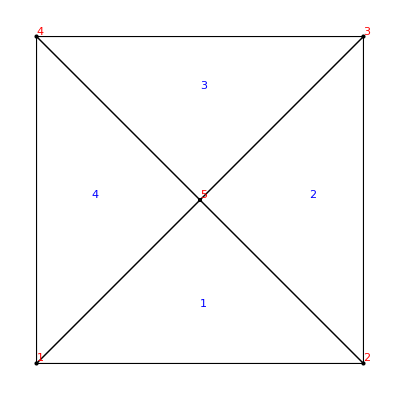

```mathematica
mesh=ToElementMesh["Coordinates"->{{0,0},{2,0},{2,2},{0,2},{1,1}},"MeshElements"-> {TriangleElement[{{1,2,5},{2,3,5},{5,3,4},{1,5,4}}]}
,"BoundaryElements"->{LineElement[{{1,2},{2,3},{3,4},{4,1}}]}
,"PointElements"->{PointElement[{{1},{2},{3},{4},{5}}]}
]
(*mesh=ToElementMesh["Coordinates"->{{0,0},{2,0},{2,2},{0,2}},"MeshElements"-> {TriangleElement[{{1,2,4},{2,3,4}}]}];*)
Show[mesh["Wireframe"["MeshElement" -> "MeshElements","MeshElementIDStyle"->Blue]],mesh["Wireframe"["MeshElement" -> "PointElements","MeshElementIDStyle"->Red]],BaseStyle->{FontSize->20}]
```

```mathematica
DefineBCs3[uVec_,tVec_,L_,mesh_]:=
Block[{tol=10^-5,IDArray},
DirichletPoints=Block[{Bttm,BttmRit,Lft,Bck,Rit,RitBttm,Tp,Nodes},
Bttm =Flatten@Position[Abs[Coords[[;;,2]]-0.0],x_/;x<tol];
(*Lft=Flatten@Position[Abs[Coords[[;;,1]]-0.0],x_/;x<tol];*)
Nodes = Join[{1,#}&/@Bttm,{2,#}&/@Bttm(*,{1,#}&/@Lft,{2,#}&/@Lft*)]
];
DirichletDof = Sort[(DirichletPoints[[;;,2]]-1)*ndof+DirichletPoints[[;;,1]]];
NeumannPoints=Block[{Tp,TpRit,Frnt,ETp,ERit,EFrnt,Nodes},
Tp=Flatten@Position[Abs[Coords[[;;,2]]-L],x_/;x<tol];
ETp=Edgedet[{0,1},mesh];
Edges={2,#}&/@ETp;
Nodes = {2,#}&/@Tp
];
NeumannDof= Sort[(NeumannPoints[[;;,2]]-1)*ndof+NeumannPoints[[;;,1]]];
DirichletVals=uVec[[#[[1]]]][Coords[[#[[2]]]]]&/@DirichletPoints;
NeumannVals=tVec[[#[[1]]]][Coords[[#[[2]]]]]&/@NeumannPoints;
IDArray=Range[ndof*nnp];
IDMat=Transpose[ArrayReshape[IDArray,{nnp,ndof}]];
IDno=Complement[IDArray,DirichletDof];
]
```

```mathematica
Radaptive[y5_]:=Block[{L=2,
Ε=10,
ν=0.499,
RelaxFactor = 1,
uVec={0.0&,0.0&}
,tVec={0.0&,1.0&}
,TracInd=True
,ConcenInd= False
},
mesh1 =ToElementMesh["Coordinates"->{{0,0},{2,0},{2,2},{0,2},{1,y5}},"MeshElements"-> {TriangleElement[{{1,2,5},{2,3,5},{5,3,4},{1,5,4}}]}
,"BoundaryElements"->{LineElement[{{1,2},{2,3},{3,4},{4,1}}]}
,"PointElements"->{PointElement[{{1},{2},{3},{4},{5}}]}];
MaterialProperty=InitializeFEM[mesh1,Ε,ν];
DefineBCs3[uVec,tVec,L,mesh1];
Print@PlotMeshBC[mesh1,DirichletPoints,NeumannPoints,ShowMesh->True,ShowNumbers->True
,ShowBCs->"NeumannBC"
(*,ShowBCs->"DirichletBC"*)
];
Fd=NewtonSolve[1,1,RelaxFactor,TracInd,ConcenInd];
PostProcess[Fd,mesh1]
]
```

```mathematica
y5List = Range[0.1,1.9,0.1]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9}

```mathematica
EnergyList = Radaptive/@y5List
```

{-0.00264579,-0.0030239,-0.0035702,-0.00440003,-0.00574539,-0.00812608,-0.0128823,-0.0241194,-0.0553791,-0.100532,-0.0553791,-0.0241194,-0.0128823,-0.00812608,-0.00574539,-0.00440003,-0.0035702,-0.0030239,-0.00264579}

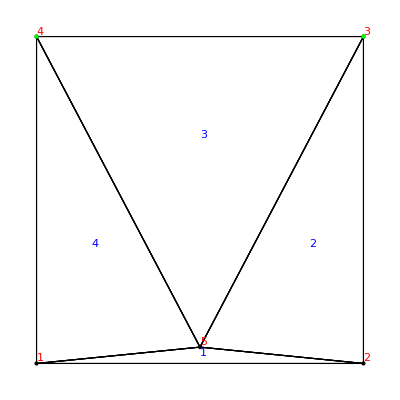

Step No. = 1

LoadFactor = 1.

Iteration: 1. 
 Norm of residual for u : 3.13985×10^-16

Compute u Converged!

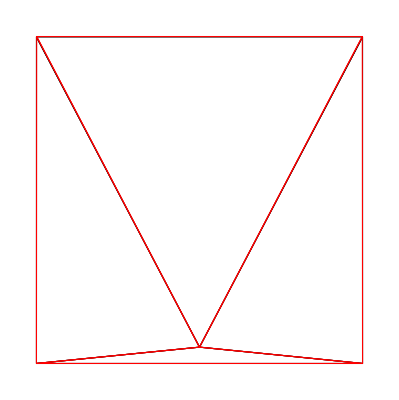

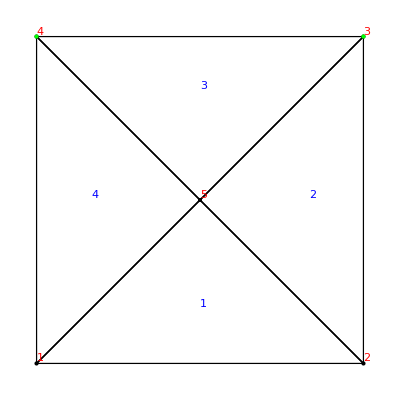

Step No. = 1

LoadFactor = 1.

Iteration: 1. 
 Norm of residual for u : 1.4766×10^-14

Compute u Converged!

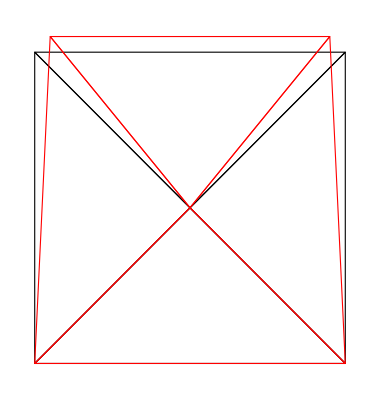

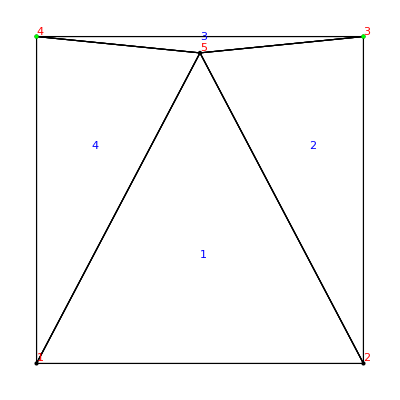

Step No. = 1

LoadFactor = 1.

Iteration: 1. 
 Norm of residual for u : 3.49113×10^-15

Compute u Converged!

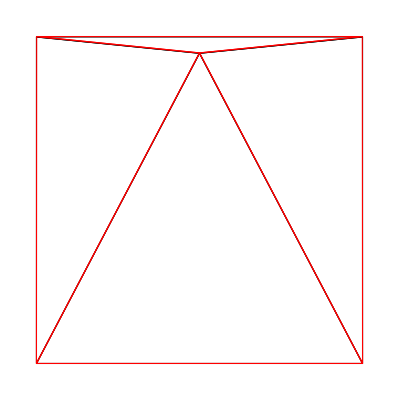

{{0.00264579,-0.00264579},{0.100532,-0.100532},{0.00264579,-0.00264579}}

```mathematica
Radaptive/@{0.1,1.0,1.9}
```

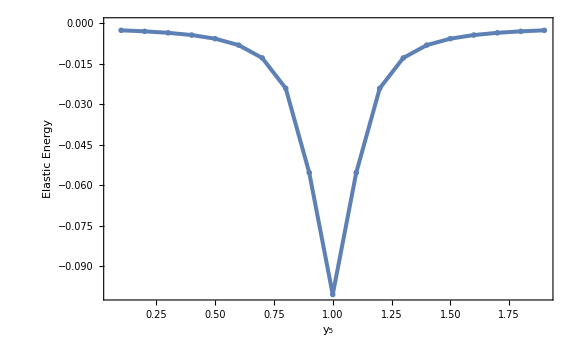

```mathematica
ListLinePlot[Transpose[{y5List,EnergyList}],PlotRange->All,PlotStyle->Directive[Thickness[0.005]],Joined->True,PlotMarkers->"OpenMarkers"
,ImageSize->Large,GridLines->None,Axes->False,AxesStyle->Directive[Black,FontFamily->"Times",24],Frame->True,FrameStyle->Directive[FontFamily->"Times",20],FrameLabel->{Style["y_5",Black,FontFamily->"Times",24],Style["Elastic Energy",Black,FontFamily->"Times",24]},RotateLabel->True
]
```